```mathematica
f[x_]=Sin[x]*Cos[x]^2;
Subscript[x, 0]=0;
Subscript[x, 1]=π/6;
Subscript[x, 2]=π/4;
Subscript[x, 3]=π/3;
Subscript[x, 4]=π/2;
Subscript[x, 5]=π;
Subscript[x, 6]=9π/5;
Subscript[x, 7]= π/5;
```

```mathematica
NN=7;
```

```mathematica
n=(NN-1)/2;
```

```mathematica
T[x_]=Subscript[a, 0]+∑_(k=1)^n (Subscript[a, k] Sin[k x] + Subscript[b, k] Cos[k x]);
```

```mathematica
eqv=Table[T[Subscript[x, j]] == f[Subscript[x, j]], {j, 0, 6}];
```

```mathematica
koef=Solve[eqv,{}]//Flatten//N
```

{a_0→4.09629×10^-17,a_1→0.25,a_2→0.,a_3→0.25,b_1→0.,b_2→0.,b_3→0.}

```mathematica
T[x_]=T[x]//.koef
```

4.09629×10^-17+0.25 Sin[x]+0.25 Sin[3 x]

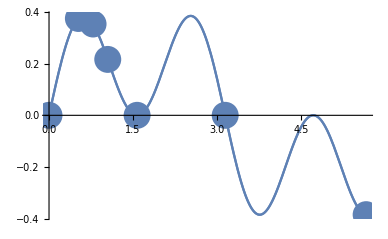

```mathematica
Gr1=ListPlot[Table[{Subscript[x, i], T[Subscript[x, i]]}, {i, 0, NN-1}],PlotStyle->{PointSize[0.05]}];
Gr2=Plot[T[x], {x,Subscript[x, 0], Subscript[x, 6]}];
Gr3=Plot[f[x], {x, Subscript[x, 0], Subscript[x, 6]}];
Show[Gr1,Gr2,Gr3,PlotRange->All]
```

```mathematica
pr=T[Subscript[x, 7]]
```

0.38471

```mathematica
toc=f[Subscript[x, 7]]//N
```

0.38471

```mathematica
a=Abs[toc-pr]
```

1.5038×10^-13

```mathematica
b=a/pr*100//Abs
```

3.90891×10^-11

```mathematica
X = {0.1, 0.2, 0.3, 0.4}
F = {1.06, 2.094, 5.908, 8.761};
n = Length[X]-1;
Do [{Subscript[x, i]= X[[i+1]], Subscript[f, i] = F[[i+1]]}, {i, 0, n}]
eqv:= Table[∑_(i=0)^n Subscript[A, i] Subscript[x, i]^j  ==D[y^j, {y, m}]/.y-> xx, {j, 0, n}]
Koef:=Solve[eqv, {}]//Flatten
P:=∑_(i=0)^n Subscript[A, i] Subscript[f, i]/.Koef
Tbl=Table[{Subscript[x,i],Subscript[f,i]},{i,0,n}]
L=InterpolatingPolynomial[Tbl,t]

P1:= D[L, {t,m}]/.t-> xx
m=1; xx= 0.1; {P, P1, P==P1}
m=1; xx=0.2;{P, P1, P==P1}
m=2; xx=0; {P, P1, P==P1}
m=3;xx=0.5; {P, P1, P==P1}
```

{0.1,0.2,0.3,0.4}

{{0.1,1.06},{0.2,2.094},{0.3,5.908},{0.4,8.761}}

8.761+(25.67+(76.65-623.5 (-0.2+t)) (-0.1+t)) (-0.4+t)

{-16.03,-16.03,True}

{30.475,30.475,True}

{1026.2,1026.2,True}

{-3741.,-3741.,True}

```mathematica
w[y_]=∏_(i=0)^n (y-Subscript[x, i])
```

(-0.4+y) (-0.3+y) (-0.2+y) (-0.1+y)

```mathematica
m=1; xx= 0.1;
R1= D[w[y], {y,m}]/.y-> xx
```

-0.006

```mathematica
m=1; xx=0.2;
```

```mathematica
R1= D[w[y], {y,m}]/.y-> xx
```

0.002

```mathematica
m=2; xx=0;
```

```mathematica
R1= D[w[y], {y,m}]/.y-> xx
```

0.7

```mathematica
m=3;xx=0.5;
```

```mathematica
R1= D[w[y], {y,m}]/.y-> xx
```

6.